```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"velocity tools","init.nb"}]];
```

#### Numeric Algorithm V1 (Via Primal Variables)

-Graphics-

```mathematica
First@Timing@Quiet@defVel[F0,1{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]
```

0.015625

0.015625

```mathematica
proj[u_]:=Projection[u,{1,0}]
```

```mathematica
x0={-1,-1};
x1={1,1};
y0Old=proj[x0];
y1Old=proj[x1];

δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr,
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/(Subscript[γ, F0][yOld-x0])];
z1=-Subscript[𝒩̂, F1][(x1-yOld)/(Subscript[γ, F1][x1-yOld])];
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[δ!=0,
If[δ>0,
y1Old=yOld;,
y0Old=yOld;
]
];
AppendTo[results,{δ,yOld}]
];
y0Old//N
,{δ,y0Old}//N]
```

{-0.538264,0.}

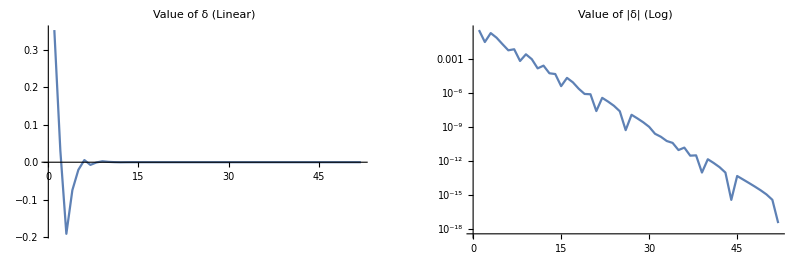

```mathematica
GraphicsRow[{
ListLinePlot[results[[;;,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[Abs[results[[;;,1]]],PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Value of |δ| (Log)"]
}]
```

```mathematica
(* plot path during fist 10 steps of algorithm *)
ListAnimate@Table[Graphics[Line[{x0,xΣ,x1}],ImageSize->Small],{xΣ,results[[;;10,2]]}]
```

#### Numeric Algorithm V2 (Using Duality)

This algorithm is currently not working.

-Graphics-

```mathematica
First@Timing@Quiet@defVel[F0,1{Cos[t],Sin[t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]
```

0.296875

0.09375

```mathematica
x0={-1,-1}//N;
x1={1,1}//N;
y0Old=proj[x0];
y1Old=proj[x1];

k=0;
δ=Infinity;
thr=$MachineEpsilon;
results={};
Monitor[
While[Abs[δ]>thr&&k<=1*^4,
k+=1;
(* Step 1 *)
yOld=(y0Old+y1Old)/2;
(* Step 2 *)
z0=Subscript[𝒩̂, F0][(yOld-x0)/(Subscript[γ, F0][yOld-x0])];
z1=-Subscript[𝒩̂, F1][(x1-yOld)/(Subscript[γ, F1][x1-yOld])];
(* Step 3 *)
δ=proj[z0+z1][[1]];
(* Step 4 *)
If[δ!=0,
If[δ>0,
v1=(𝒩̂)_(F1^°)[z1];
y1Old=δ proj[v1];,
v0=(𝒩̂)_(F0^°)[z0];
y0Old=δ proj[v0];
]
];
AppendTo[results,{δ,yOld,y1Old,y0Old}]
];
y0Old//N
,{δ,yOld,y0Old,y1Old,k}//N]
```

{-0.0464664,0.}

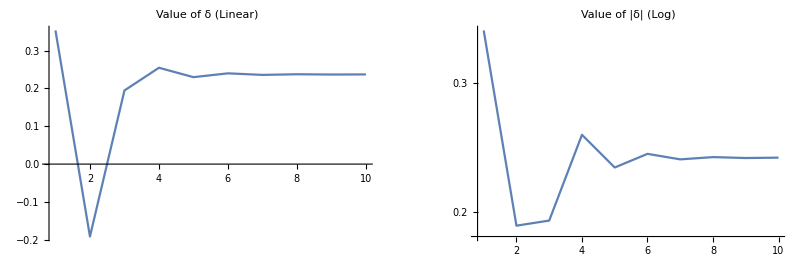

```mathematica
maxK=10;
GraphicsRow[{
ListLinePlot[results[[;;maxK,1]],PlotRange->All,
PlotLabel->"Value of δ (Linear)"],
ListLinePlot[Abs[results[[;;maxK,1]]],PlotRange->All,ScalingFunctions->"Log",
PlotLabel->"Value of |δ| (Log)"]
}]
```

#### Exact Solution Derivation

```mathematica
First@Timing@Quiet@defVel[F0,{Cos[t],Sin [t]}]
First@Timing@Quiet@defVel[F1,2{Cos[t],Sin[t]}]

x0={-1,-1};
x1={1,1};
```

0.03125

0.015625

We can find the scaled normal cone of F1 from x0 at any point in space.

```mathematica
(𝒩̂)_(F1^°)[{x,y}-x0]
```

{(2 (1+x))/(√((1+x)^2+(1+y)^2)),(2 (1+y))/(√((1+x)^2+(1+y)^2))}

This plot shows the x-component of the dual vectors ζ_0 and ζ_1 along the interface Σ. The sum of these components is shown in green.

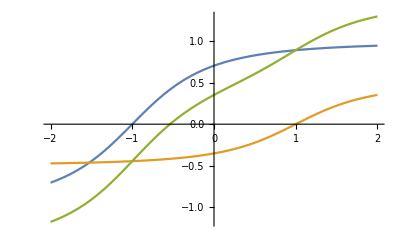

```mathematica
Plot[{
Subscript[𝒩̂, F0][{x,0}-x0][[1]],
-Subscript[𝒩̂, F1][x1-{x,0}][[1]],
Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]
},{x,-2,2}]
```

Where these curves are equal opposites is optimal crossing point, which can be solved exactly.

```mathematica
Subscript[𝒩̂, F0][{x,0}-x0][[1]]-Subscript[𝒩̂, F1][x1-{x,0}][[1]]
x/.Solve[%==0,x]
xOpt=First@Select[%,Im[#]==0&]
%//N
```

-(1-x)/(2 √(1+(1-x)^2))+(1+x)/(√(1+(1+x)^2))

{-1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))+1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))}

-1/6 √(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))+1/2 √(4/3-1/9 (5967-216 √519)^(1/3)-1/3 (221+8 √519)^(1/3)+20/(√(6+(5967-216 √519)^(1/3)+3 (221+8 √519)^(1/3))))

-0.538264

What is the optimal travel time?

```mathematica
xΣ={xOpt,0};
t0=Subscript[γ, F0][xΣ-x0];
t1=Subscript[γ, F1][x1-xΣ];
T=t0+t1//N
```

2.01882

How does this fit in the previously computable solutions?

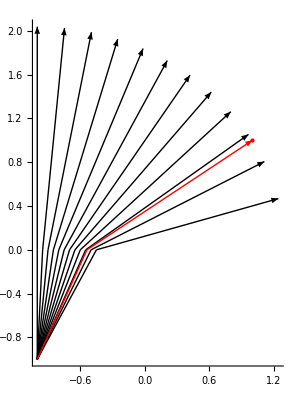

```mathematica
raytracePlt=Show[Graphics[{
Arrowheads[Small],
Table[
Module[{T=T,t,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* properly scaled normal cone points *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=discretize/@Select[(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}],Black,Arrow[{x0,x0+T v0}]}
]&/@v2s

],
{t0,-1,.5,0.05}
]},Axes->True]];
Show[raytracePlt,Graphics[{Red,Arrow[{x0,xΣ,x1}],Point[{1,1}]}]]
```